```mathematica
e=1;
m=1;
```

```mathematica
BE=10;
B=2;
BS=1;
phi=5;
phiS=0;
phiE=10;
```

```mathematica
CEsq:=BE/B-1;
CSsq:=1-BS/B;
DEsq:=2 e/m (phi-phiS);
DSsq:=2e/m(phiE-phi);
```

#### Regions A & B

```mathematica
regionAPos:=CEsq vPerp^2 -vPar^2 ≤DEsq&&vPar≥0;
regionA:=CEsq vPerp^2 -vPar^2 ≤DEsq;
regionANeg:=CEsq vPerp^2 -vPar^2 ≤DEsq&&vPar≤0;
regionB:=CSsq vPerp^2 +vPar^2 ≥DSsq;
E1:=regionANeg&&regionB;
S1:=regionAPos&&regionB;
T:=(!regionA)&&(!regionB);
E2:=regionA&&(!regionB)
S2:=(!regionA)&&regionB;
```

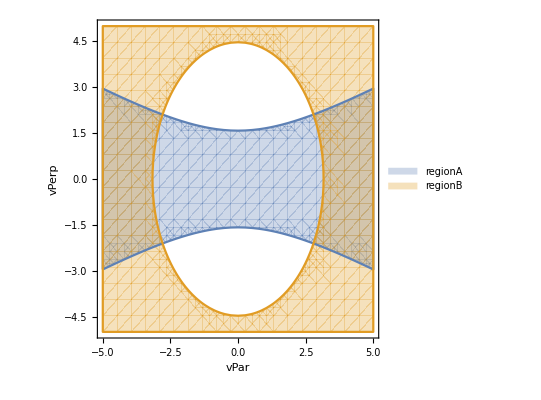

```mathematica
RegionPlot[{regionA,regionB},{vPar,-5,5},{vPerp,-5,5},PlotLegends->"Expressions",
Frame->True,FrameLabel->{"vPar","vPerp"}]
```

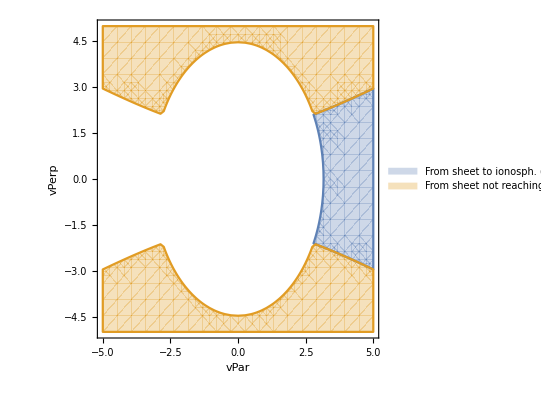

```mathematica
Splots=RegionPlot[{S1,S2},{vPar,-5,5},{vPerp,-5,5},PlotLegends->{"From sheet to ionosph. (S_1)","From sheet not reaching ionosph. (S_2)"} ,
Frame->True,FrameLabel->{"vPar","vPerp"}]
```

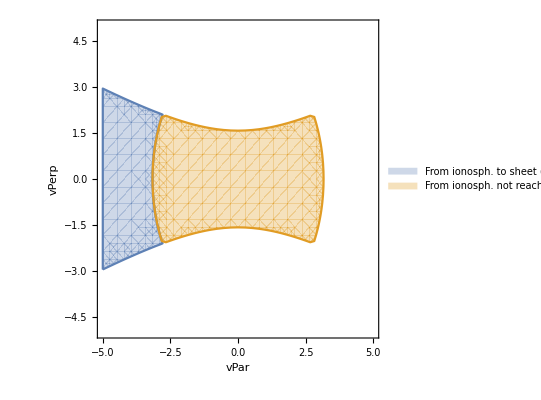

```mathematica
Eplots=RegionPlot[{E1,E2},{vPar,-5,5},{vPerp,-5,5},PlotLegends->{"From ionosph. to sheet (E_1)","From ionosph. not reaching sheet (E_2)"},
Frame->True,FrameLabel->{"vPar","vPerp"}]
```

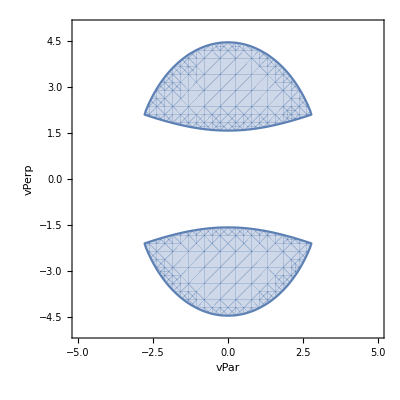

```mathematica
Tplot=RegionPlot[T,{vPar,-5,5},{vPerp,-5,5},PlotLegends->"Trapped",
Frame->True,FrameLabel->{"vPar","vPerp"}]
```

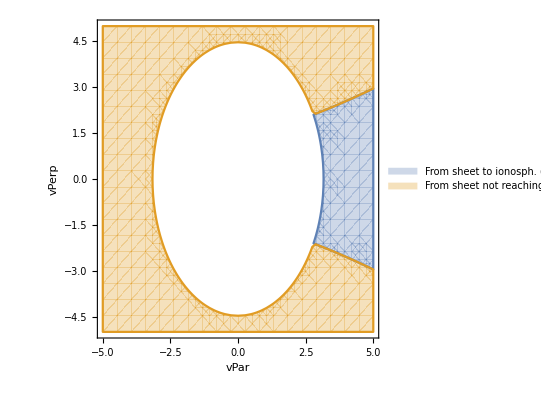
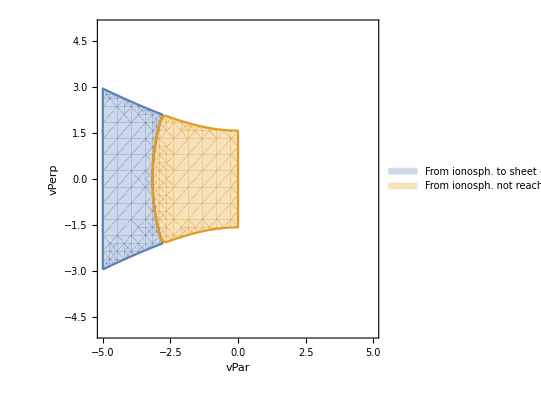
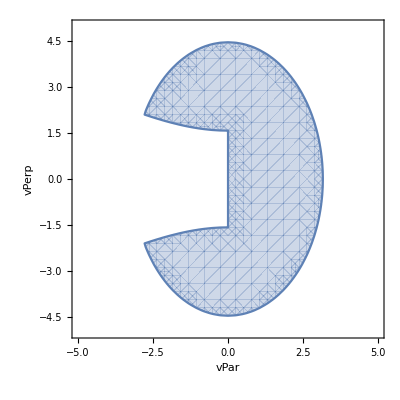

```mathematica
Column[{Splots,Eplots,Tplot}]
```

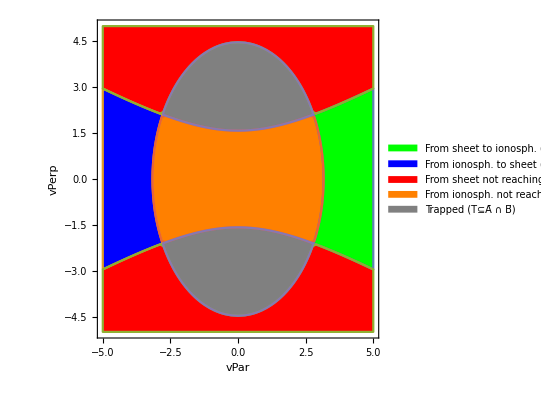

```mathematica
allPlots=RegionPlot[{S1,E1,S2,E2,T},{vPar,-5,5},{vPerp,-5,5},PlotLegends->{"From sheet to ionosph. (S_1⊆A ∩ B ∩ v_(||)>0)","From ionosph. to sheet (E_1⊆A ∩ B ∩ v_(||)<0)","From sheet not reaching ionosph. (S_2⊆Ā ∩ B)","From ionosph. not reaching sheet (E_2⊆A ∩ B̄)","Trapped (T⊆Ā ∩ B̄)"} ,PlotStyle->{Green,Blue,Red,Orange,Gray},
Frame->True,FrameLabel->{"vPar","vPerp"}]
```